```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
SetDirectory[NotebookDirectory[]];
Needs["gUtils`"];
Needs["gBRDF`"];
Needs["sgCommon`"];
Needs["gPlots`"];
Needs["gPlots3D`"];
Needs["gSphericalCap`"];


f1=ⅇ^(-λ Sin[θ]^2) Cos[θ];
jaco1=(θ1+θL)/(θL+ArcTan[Sec[θ1] (k+Sin[θ1])])/.{k->Max[Sec[θ+θ1] Sin[θ],0]};g
jaco1//FullSimplify
f2=Csc[1/2 (θL+ArcTan[k Sec[θ1]+Tan[θ1]])] Sin[(θ1+θL)/2]/.{k->Max[Sec[θ+θ1] Sin[θ],0]};
f2//FullSimplify


(*Manipulate[Plot[ⅇ^(-λ Sin[θ]^2) Cos[θ],{θ,0,0.3}],{λ,sgMinLambda,500}]*)

Manipulate[Plot[
	{
		(θ1+θL)/(θL+ArcTan[Sec[θ1] (Max[0,Sec[θ+θ1] Sin[θ]]+Sin[θ1])])*Csc[1/2 (θL+ArcTan[Sec[θ1] (Max[0,Sec[θ+θ1] Sin[θ]]+Sin[θ1])])] Sin[(θ1+θL)/2],
		(ⅇ^(-λ Sin[θ]^2) Cos[θ])/.{λ->(-0.649+0.351*Cos[θ1] *Csc[(θ1+θL)/2]^2)}
	},
	{θ,0,π/2},
	PlotRange->{{0,π/2},{0,1}}],
	{θ1,0,π/2},{θL,0,π/2}]
(*Quiet@FindMinimum[NIntegrate[Abs[f1-f2],{m,0.0001,1},{θ,-π/2,π/2},
	PrecisionGoal->1,AccuracyGoal->1, Method->"QuasiMonteCarlo",MaxRecursion->2],{a,1/π},{b,2},{c,1}]*)
```

g

(θ1+θL)/(θL+ArcTan[Sec[θ1] (Max[0,Sec[θ+θ1] Sin[θ]]+Sin[θ1])])

Csc[1/2 (θL+ArcTan[Sec[θ1] (Max[0,Sec[θ+θ1] Sin[θ]]+Sin[θ1])])] Sin[(θ1+θL)/2]

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
asgPolar[θ,π/2-θ,π/2,λ,μ,1]
```

ⅇ^(-λ Sin[θ]^2) Cos[θ]

```mathematica
(*Sin[θ1]=h2/k;*)
d1=Tan[θ];
h1=Tan[θ1]*Tan[θ];
Tan[θ]==d2/h2;
h1/h2==d1/(d1+d2);

(Tan[θ1]*Tan[θ])/(d2 Tan[θ])==Tan[θ]/(Tan[θ]+d2)
```

Tan[θ1]/d2==Tan[θ]/(d2+Tan[θ])

```mathematica
Solve[h1/h2==d1/(d1+d2),d2]
```

{{d2→h2 Cot[θ1]-Tan[θ]}}

```mathematica
Integrate[ⅇ^(-λ Sin[θ]^2) Cos[θ],{θ,0,π/4}]
(*Integrate[(Csc[1/2 (θL+ArcTan[Sec[θ1]^2 Tan[θ]+Tan[θ1]])] Sin[(θ1+θL)/2]),{θ,0,π/2}];*)
Integrate[(1-1/2 θ Cot[(θ1+θL)/2]),{θ,0,π/4}]
(*Solve[(ⅇ^(-λ Sin[θ]^2) Cos[θ]==Csc[1/2 (θL+θ1+(Sec[θ1]^2 *θ)/(1+Tan[θ1]^2))] Sin[(θ1+θL)/2])/.{θ->0.1},λ]*)
Solve[((√π)/(2 √λ)==π/4-1/64 π^2 Cot[(θ1+θL)/2]),λ]
```

(√π Erf[(√λ)/(√2)])/(2 √λ)

π/4-1/64 π^2 Cot[(θ1+θL)/2]

{{λ→1024/(π (-16+π Cot[(θ1+θL)/2])^2)}}

```mathematica
Erf[0.1]//N
```

0.112463

```mathematica
Series[ArcTan[Tan[x]*a+b],{x,0,1}]
```

ArcTan[b]+(a x)/(1+b^2)+O[x]^2

```mathematica
(Csc[1/2 (θL+θ1+(Sec[θ1]^2 *θ)/(1+Tan[θ1]^2))] Sin[(θ1+θL)/2])//FullSimplify
```

Csc[1/2 (θ+θ1+θL)] Sin[(θ1+θL)/2]

```mathematica
Csc[1/2 (θ+θ1+θL)] Sin[(θ1+θL)/2];
Sin[x]/Sin[x+y]
```

Csc[x+y] Sin[x]

```mathematica
Series[Csc[1/2 (θ+θ1+θL)] ,{θ,0,1}]
```

Csc[(θ1+θL)/2]-1/2 (Cot[(θ1+θL)/2] Csc[(θ1+θL)/2]) θ+O[θ]^2

```mathematica
Sin[(θ1+θL)/2]*(Csc[(θ1+θL)/2]-1/2 (Cot[(θ1+θL)/2] Csc[(θ1+θL)/2]) θ)//FullSimplify
```

1-1/2 θ Cot[(θ1+θL)/2]

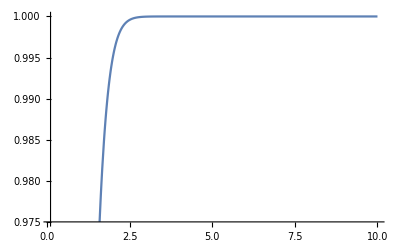

```mathematica
Plot[Erf[x],{x,0.1,10}]
```

```mathematica
Erf[1.5]//N
```

0.966105

```mathematica
Quiet@FindMinimum[NIntegrate[Abs[
		(θ1+θL)/(θL+ArcTan[Sec[θ1]^2 Tan[θ]+Tan[θ1]])*Csc[1/2 (θL+ArcTan[Sec[θ1]^2 Tan[θ]+Tan[θ1]])] Sin[(θ1+θL)/2]-
		(ⅇ^(-λ Sin[θ]^2)Cos[θ]/.{λ->a+b*Cos[θ1]/(c+Sin[(θ1+θL)/2]^2)})

	],{θ,0.001,π/2-0.001},{θ1,0.001,π/2-0.001},{θL,0.001,π/2},
	PrecisionGoal->1,AccuracyGoal->1, Method->"QuasiMonteCarlo",MaxRecursion->2],
	{a,1},{b,1},{c,1},{d,1},{e,1},{f,1}]
```

{0.696447,{a→-0.861915,b→1.31936,c→0.443104,d→1.,e→1.,f→1.}}

```mathematica
(*(0.098+2.213 Cos[θ1])/(6.639-6.015Cos[(θ1+θL)/2])*)
(a+b*Cos[θ1]/(c+Sin[(θ1+θL)/2]^2))/.{a->-0.8619154273250967,b->1.3193577075500125,c->0.44310365005583274,d->1.,e->1.,f->1.}
```

-0.861915+(1.31936 Cos[θ1])/(0.443104+Sin[(θ1+θL)/2]^2)

```mathematica
Manipulate[Plot[0.075+0.884 Cos[θ1] Cot[(θ1+θL)/2],{θ1,0,π/2}],{θL,0,π/2}]
```

{3.70353,{θ1→-9.44572×10^-10,θL→1.18674×10^-9}}

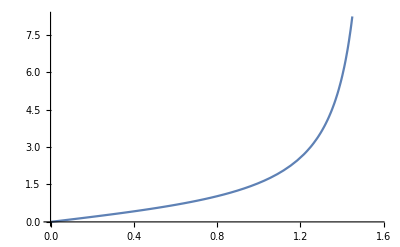

```mathematica
Plot[Tan[x],{x,0,π/2}]
```